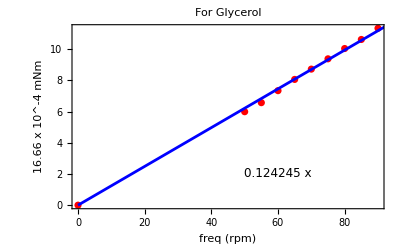

```mathematica
data={{0,0},{50,5.99},{55,6.57},{60,7.34},{65,8.06},{70,8.72},{75,9.38},{80,10.04},{85,10.62},{90,11.34}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Glycerol",Epilog->{Text[Style[eqn,12],{60,2}]}]
```

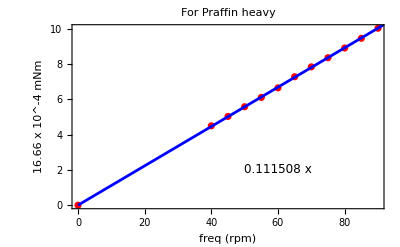

```mathematica
data={{0,0},{40,4.5},{45,5.03},{50,5.58},{55,6.11},{60,6.65},{65,7.28},{70,7.84},{75,8.36},{80,8.91},{85,9.46},{90,10.03}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Praffin heavy",Epilog->{Text[Style[eqn,12],{60,2}]}]
```

```mathematica
ClearAll["Global"]
```

ListPlot::lpn: Pattern[(#1&)[data],_seaback] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[data_seaback,PlotStyle→color],,Frame→True,FrameLabel→{Temperature (°C),Voltage (mV)},PlotLabel→Seebeck Coefficient,Epilog→{Text[0.0506786 x-0.888214,{140,6}]}].

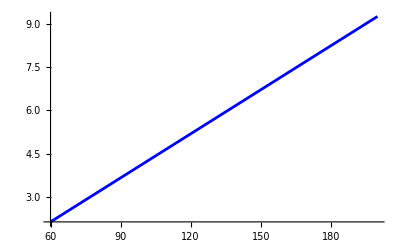
Show[ListPlot[data_seaback,PlotStyle→RGBColor[1, 0, 0]],-Graphics-,Frame→True,FrameLabel→{Temperature (°C),Voltage (mV)},PlotLabel→Seebeck Coefficient,Epilog→{Text[0.0506786 x-0.888214,{140,6}]}]

```mathematica
data={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};

(*Proper linear fit with intercept*)
fit=Fit[data,{1,x},x];

Show[ListPlot[data_seaback,PlotStyle->Red],Plot[fit,{x,60,200},PlotStyle->Blue],Frame->True,FrameLabel->{"Temperature (°C)","Voltage (mV)"},PlotLabel->"Seebeck Coefficient",Epilog->{Text[Style[ToString[fit,TraditionalForm],12],{140,6}]}]
```

best equation Get line of the^2 (-0.888214+0.0506786 x)

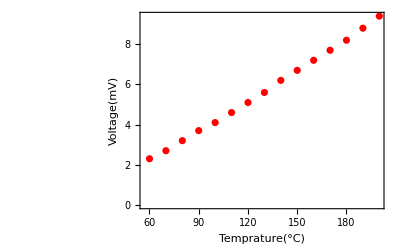

```mathematica
data2={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};
fit2=LinearModelFit[data2,x,x];
eqn2=fit2["BestFit"];(Get the equation of the best fit line)
Show[ListPlot[data2,PlotStyle->Red],Plot[fit2[x],{x,0,20},PlotStyle->Blue],Frame->True,FrameLabel->{"Temprature(°C)","Voltage(mV)"},Epilog->Inset[Style[eqn2,12],{6,-0.5}]]
```

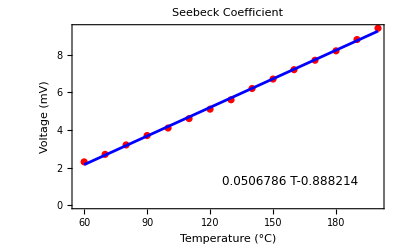

```mathematica
data2={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};
fit2=LinearModelFit[data2,{T},T];  (*Replace x with T*)
eqn2=fit2["BestFit"];

Show[ListPlot[data2,PlotStyle->Red],Plot[fit2[T],{T,60,200},PlotStyle->Blue],Frame->True,FrameLabel->{"Temperature (°C)","Voltage (mV)"},PlotLabel->"Seebeck Coefficient",Epilog->Inset[Style[eqn2,12],Scaled[{0.7,0.15}]]]
```

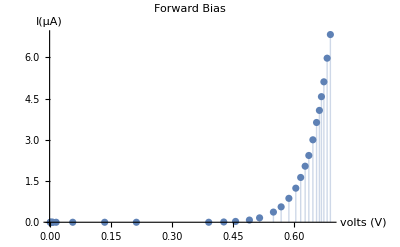

```mathematica
ListPlot[{{0.0017,0},{0.0023,0},{0.0036,0},{0.007,0},{0.0077,0},{0.0160,0},{0.0568,0},{0.1353,0},{0.2132,0},{0.3910,0},{0.4280,0.01},{0.457,0.03},{0.491,0.08},{0.516,0.16},{0.550,0.37},{0.569,0.56},{0.588,0.87},{0.605,1.24},{0.617,1.63},{0.628,2.04},{0.637,2.43},{0.647,3},{0.656,3.63},{0.663,4.07},{0.668,4.57},{0.674,5.11},{0.682,5.97},{0.690,6.83}},Filling->Axis,PlotLabel->"Forward Bias",AxesLabel->{"volts (V)","I(μA)"}]
```

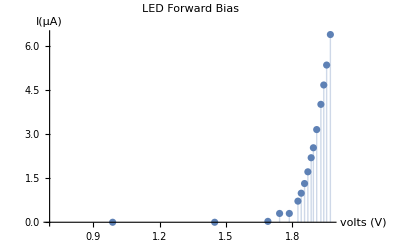

```mathematica
(*led forwrd bias*)
ListPlot[{{0.001,0},{0.101,0},{0.987,0},{1.449,0},{1.690,0.03},{1.743,0.3},{1.787,0.3},{1.826,0.72},{1.841,0.99},{1.856,1.32},{1.871,1.72},{1.886,2.20},{1.896,2.54},{1.911,3.16},{1.930,4.02},{1.943,4.68},{1.956,5.36},{1.973,6.40}},Filling->Axis,PlotLabel->"LED Forward Bias",AxesLabel->{"volts (V)","I(μA)"}]
```

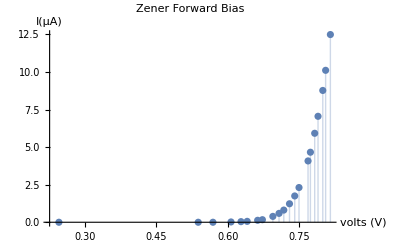

```mathematica
(*zenner forwrd bias*)
ListPlot[{{0.001,0},{0.245,0},{0.538,0},{0.569,0},{0.607,0.02},{0.628,0.04},{0.641,0.06},{0.663,0.13},{0.673,0.17},{0.695,0.39},{0.708,0.59},{0.718,0.81},{0.730,1.23},{.741,1.75},{0.750,2.31},{0.769,4.08},{0.774,4.66},{.783,5.92},{0.790,7.05},{0.800,8.77},{0.806,10.11},{0.816,12.49}},Filling->Axis,PlotLabel->"Zener Forward Bias",AxesLabel->{"volts (V)","I(μA)"}]
```

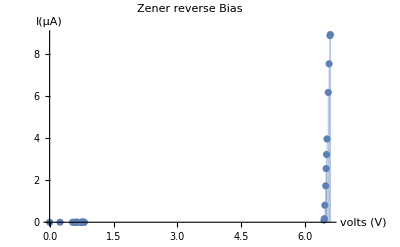

```mathematica
(*Zener reverse*)
ListPlot[{{0.001,0},{0.245,0},{0.538,0},{0.569,0},{0.607,0},{0.628,0},{0.641,0},{0.663,0},{.741,0},{0.750,0},{0.769,0},{0.774,0},{.783,0},{0.790,0},{0.800,0},{0.806,0},{0.816,0},{6.44,.1},{6.45,0.17},{6.46,.81},{6.48,1.73},{6.49,2.55},{6.50,3.22},{6.51,3.96},{6.54,6.17},{6.56,7.53},{6.58,8.87},{6.59,8.92}},Filling->Axis,PlotLabel->"Zener reverse Bias",AxesLabel->{"volts (V)","I(μA)"}]
```